# PreModule

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ42]]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

# Figure

## Module

LevTest

```mathematica
Lev4DoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,Sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Range[-0.01,0.01,0.00005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(Sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

(*Re[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Re[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]*)
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]
]
```

```mathematica
Lev3DoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.00005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]
,
(*
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],*)
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]
```

```mathematica
Lev3xsingleDoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.0002])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]
,
If[ab==2,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,0,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}]
]]
```

```mathematica
Lev3xsingleDoppTestsc2Sep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.0002])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc2,c,ℏ,e0,u,Nat,d42]]
,
If[ab==2,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,0,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}]
]]
```

```mathematica
Lev3xsingleDoppTestsc3Sep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.0002])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]
,
If[ab==2,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,0,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}]
]]
```

TvS

```mathematica
fil[list_]:=Select[list,-10^-10≤ #&&#∈Reals&]
Off[Power::infy]
Off[Infinity::indet]
```

```mathematica
step=0.05;
end=4;
p=15.865;
Clear[max3,max4]
max3[i_]:=Mean[fil[Lev3DoppTestscSep[100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a1={Table[{i/(Rbpress[100][[2]]*10^-9),1-Min[fil[Lev3DoppTestscSep[100,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0.001,end,step}], Table[{i/(Rbpress[100][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[100,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.001,end,step}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[50,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[50,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a2={Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3DoppTestscSep[50,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0.001,end,step}], Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[50,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.001,end,step}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[20,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[20,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a3={Table[{i/(Rbpress[20][[2]]*10^-9),1-Min[fil[Lev3DoppTestscSep[20,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0.001,end,step}], Table[{i/(Rbpress[20][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[20,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.001,end,step}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[200,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[200,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a4={Table[{i/(Rbpress[200][[2]]*10^-9),1-Min[fil[Lev3DoppTestscSep[200,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0.001,end,step}], Table[{i/(Rbpress[200][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[200,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.001,end,step}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[400,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[400,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a5={Table[{i/(Rbpress[400][[2]]*10^-9),1-Min[fil[Lev3DoppTestscSep[400,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,end,step}], Table[{i/(Rbpress[400][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[400,p/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.001,end,step}]};
```

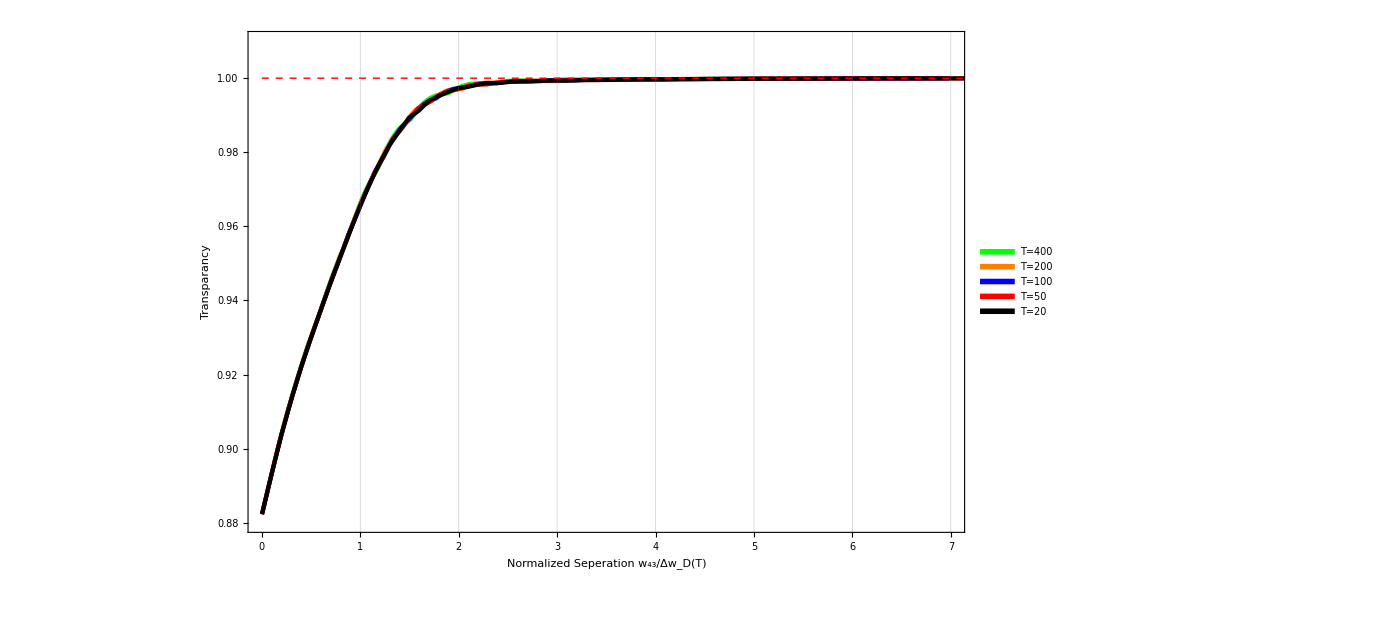

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=200",Orange],Style["T=100",Blue],Style["T=50",Red],Style["T=20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMM2=ListPlot[{a5[[2]],a4[[2]],a1[[2]],a2[[2]],a3[[2]]},PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black}}
,PlotRange->{{0,7},{0.88,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

```mathematica
Export["fianl2435r.jpg",Hubrama]
```

fianl2435r.jpg

# γ=1.5MHZ

```mathematica
γ=1.438;
p=15.865;
step=0.05;
end=2;
max3[i_]:=Mean[Lev3DoppTestscSep[100,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max4[i_]:=Mean[Lev4DoppTestscSep[100,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max5[i_]:=Mean[Lev3x1DoppTestscSep[100,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
a1={Table[{i/(Rbpress[100][[2]]*10^-9),1-Min[Lev3DoppTestscSep[100,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]/max3[i]},{i,0.0001,end,step}], Table[{i/(Rbpress[100][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[100,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.0001,end,step}],
Table[{i/(Rbpress[100][[2]]*10^-9),1-Min[fil[Lev3x1DoppTestscSep[100,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max5[i]},{i,0.0001,end,step}]
};
Print["1th"]
max3[i_]:=Mean[Lev3DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max4[i_]:=Mean[Lev4DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max5[i_]:=Mean[Lev3x1DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
a2={Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[Lev3DoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]/max3[i]},{i,0.0001,end,step}], Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.0001,end,step}],
Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3x1DoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max5[i]},{i,0.0001,end,step}]
};
max3[i_]:=Mean[Lev3DoppTestscSep[20,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max4[i_]:=Mean[Lev4DoppTestscSep[20,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max5[i_]:=Mean[Lev3x1DoppTestscSep[20,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
a3={Table[{i/(Rbpress[20][[2]]*10^-9),1-Min[Lev3DoppTestscSep[20,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]/max3[i]},{i,0.0001,end,step}], Table[{i/(Rbpress[20][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[20,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.0001,end,step}],Table[{i/(Rbpress[20][[2]]*10^-9),1-Min[fil[Lev3x1DoppTestscSep[20,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max5[i]},{i,0.0001,end,step}]
};
Print["3th"]
max3[i_]:=Mean[Lev3DoppTestscSep[200,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max4[i_]:=Mean[Lev4DoppTestscSep[200,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max5[i_]:=Mean[Lev3x1DoppTestscSep[200,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
a4={Table[{i/(Rbpress[200][[2]]*10^-9),1-Min[Lev3DoppTestscSep[200,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]/max3[i]},{i,0.0001,end,step}], Table[{i/(Rbpress[200][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[200,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.0001,end,step}],Table[{i/(Rbpress[200][[2]]*10^-9),1-Min[fil[Lev3x1DoppTestscSep[200,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max5[i]},{i,0.0001,end,step}]
};
max3[i_]:=Mean[Lev3DoppTestscSep[400,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max4[i_]:=Mean[Lev4DoppTestscSep[400,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max5[i_]:=Mean[Lev3x1DoppTestscSep[400,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
a5={Table[{i/(Rbpress[400][[2]]*10^-9),1-Min[Lev3DoppTestscSep[400,50/1000,1/1000,γ*10^6,0,0,0,i*1000]]/max3[i]},{i,0.0001,end,step}], Table[{i/(Rbpress[400][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[400,50/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.0001,end,step}],Table[{i/(Rbpress[400][[2]]*10^-9),1-Min[fil[Lev3x1DoppTestscSep[400,50/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max5[i]},{i,0.0001,end,step}]
};
```

1th

3th

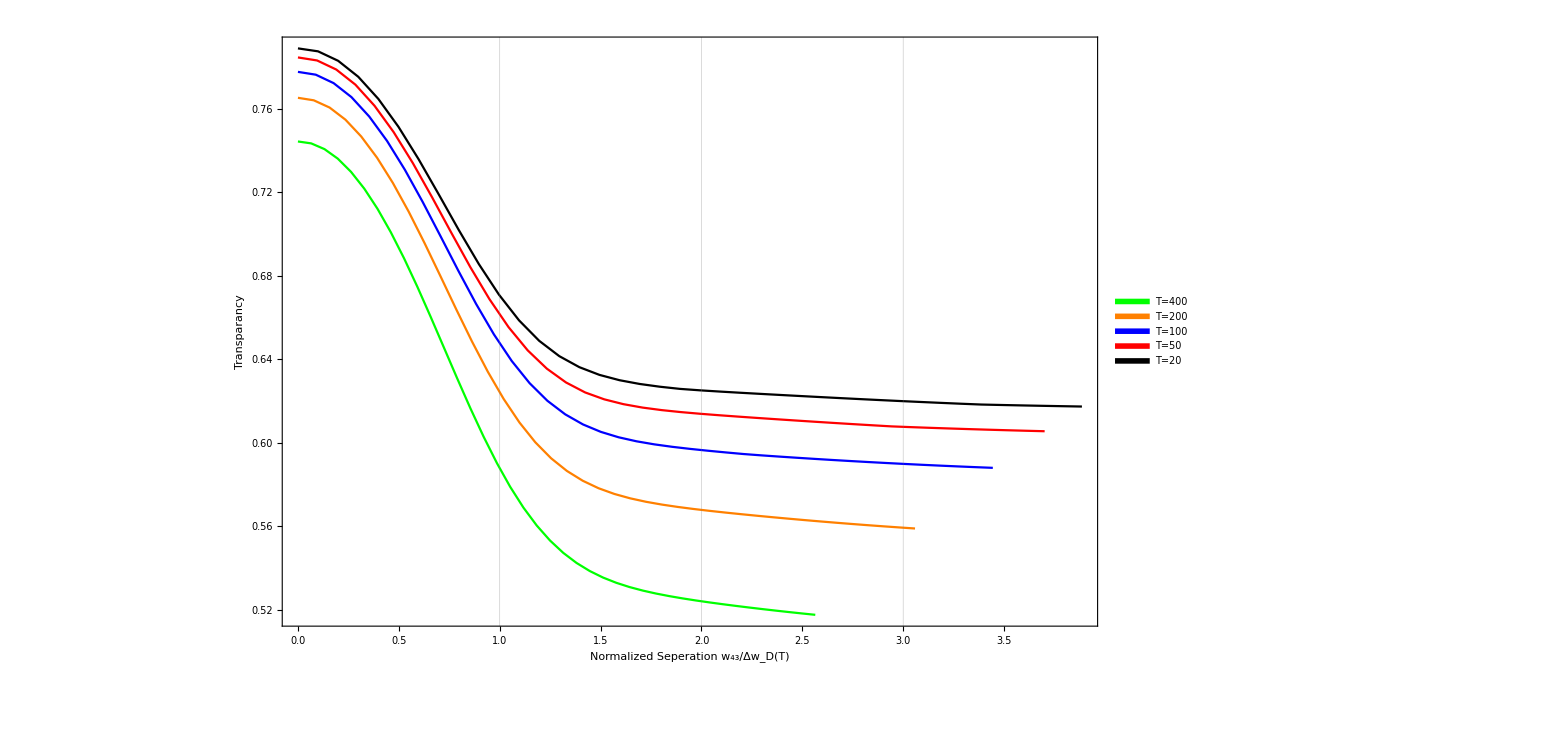

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black},AbsoluteThickness[5]]],{Style["T=400",Green],Style["T=200",Orange],Style["T=100",Blue],Style["T=50",Red],Style["T=20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
ListPlot[{a5[[2]],a4[[2]],a1[[2]],a2[[2]],a3[[2]]},PlotLegends->Placed[legend,{Right,Center}],ImageSize->1200,Joined->True,PlotStyle->{Green,Orange,Blue,Red,Black},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[30],GridLines->{{1,2,3},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

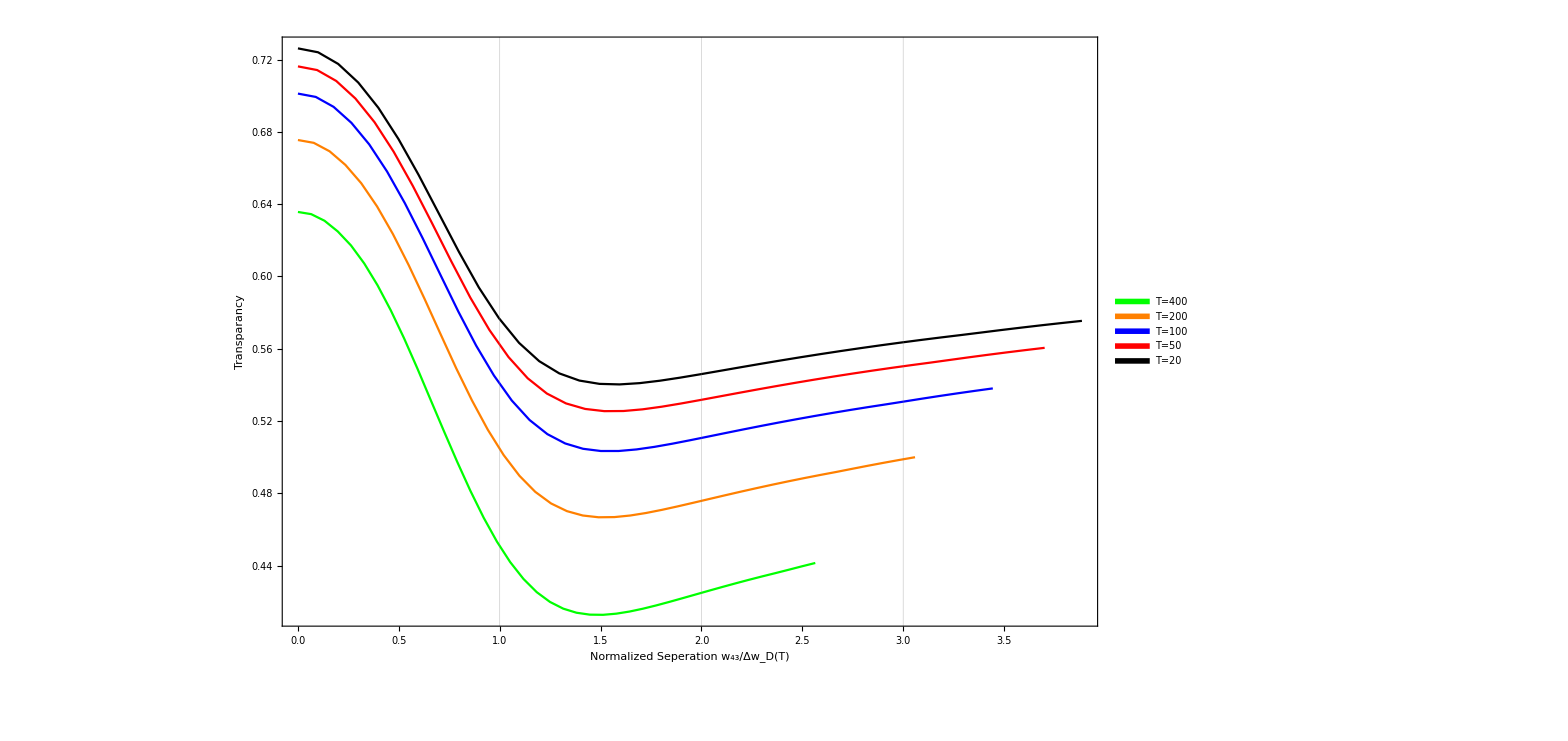

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black},AbsoluteThickness[5]]],{Style["T=400",Green],Style["T=200",Orange],Style["T=100",Blue],Style["T=50",Red],Style["T=20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
ListPlot[{a5[[1]],a4[[1]],a1[[1]],a2[[1]],a3[[1]]},PlotLegends->Placed[legend,{Right,Center}],ImageSize->1200,Joined->True,PlotStyle->{Green,Orange,Blue,Red,Black},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[30],GridLines->{{1,2,3},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

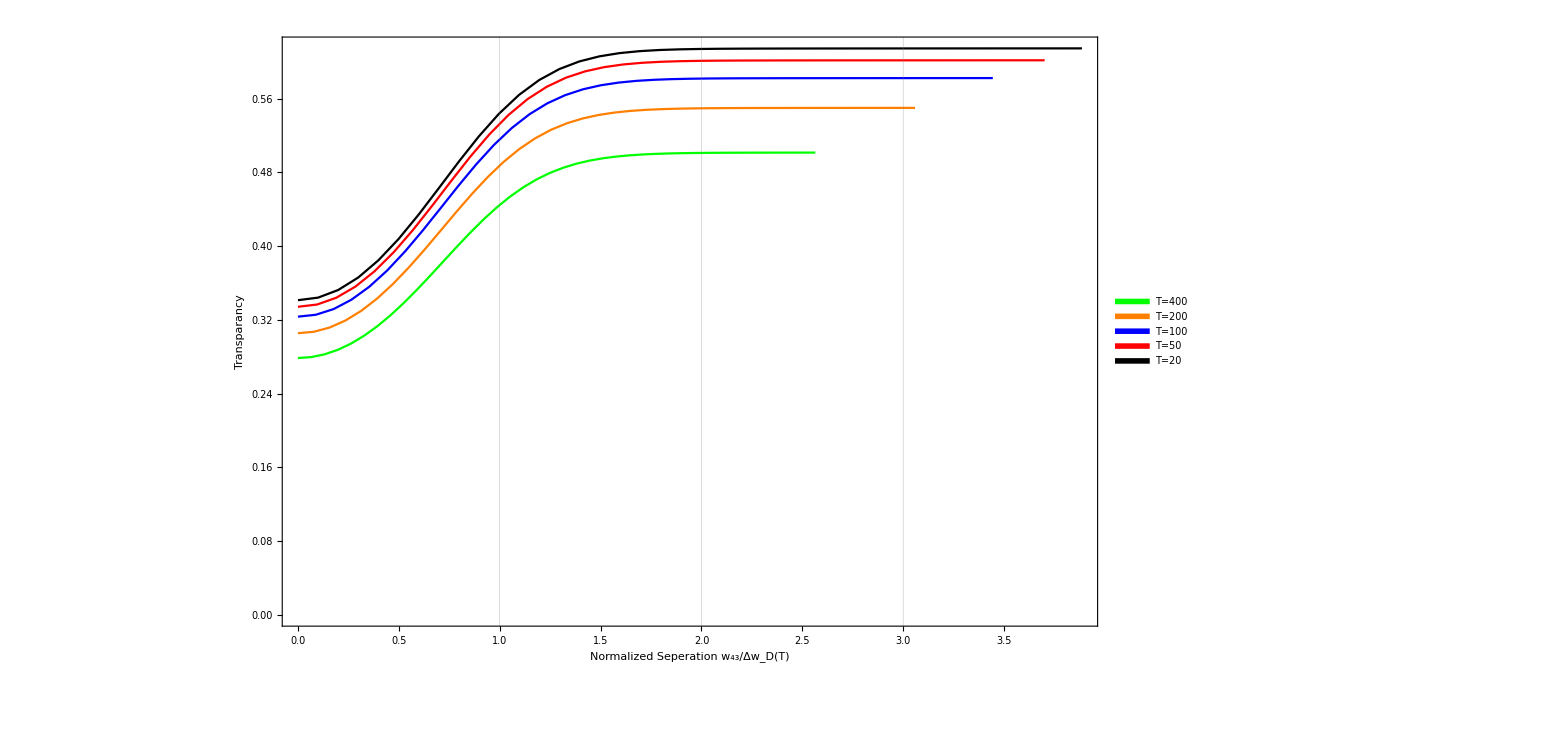

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black},AbsoluteThickness[5]]],{Style["T=400",Green],Style["T=200",Orange],Style["T=100",Blue],Style["T=50",Red],Style["T=20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
ListPlot[{a5[[3]],a4[[3]],a1[[3]],a2[[3]],a3[[3]]},PlotLegends->Placed[legend,{Right,Center}],ImageSize->1200,Joined->True,PlotStyle->{Green,Orange,Blue,Red,Black},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[30],GridLines->{{1,2,3},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

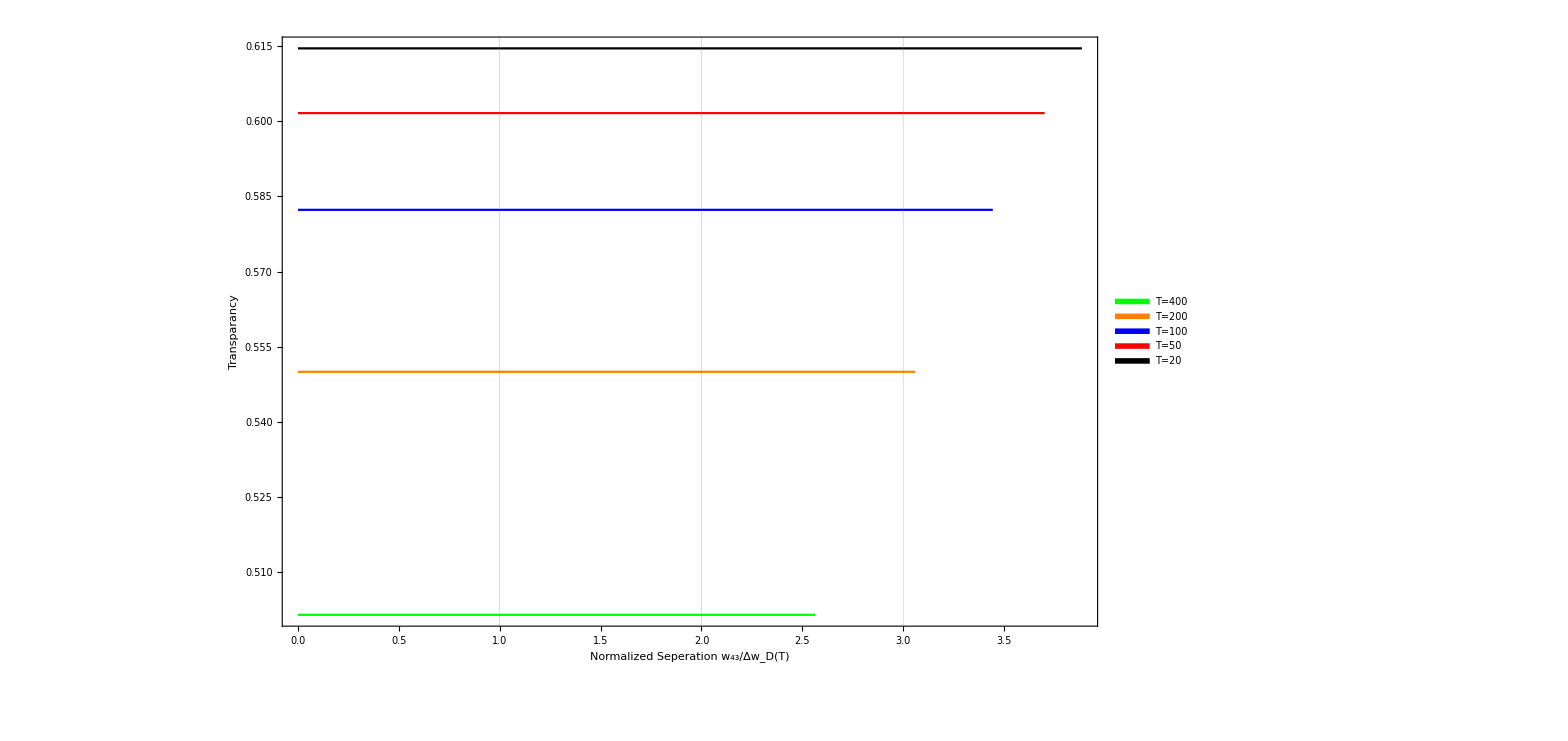

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black},AbsoluteThickness[5]]],{Style["T=400",Green],Style["T=200",Orange],Style["T=100",Blue],Style["T=50",Red],Style["T=20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
ListPlot[{a5[[4]],a4[[4]],a1[[4]],a2[[4]],a3[[4]]},PlotLegends->Placed[legend,{Right,Center}],ImageSize->1200,Joined->True,PlotStyle->{Green,Orange,Blue,Red,Black},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[30],GridLines->{{1,2,3},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
γ=1.438;
step=0.05;
end=4;
p=15.865;
max3[i_]:=Mean[Lev3DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
max4[i_]:=Mean[Lev4DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
max5[i_]:=Mean[Lev3xsingleDoppTestsc2Sep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
max6[i_]:=Mean[Lev3xsingleDoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
max7[i_]:=Mean[Lev3xsingleDoppTestsc3Sep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];

a2={Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[Lev3DoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]/max3[i]},{i,0.0001,end,step}], Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.0001,end,step}],
Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3xsingleDoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max5[i]},{i,0.0001,end,step}],
Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3xsingleDoppTestsc2Sep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max6[i]},{i,0.0001,end,step}]
};
```

```mathematica
a23=Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3xsingleDoppTestsc2Sep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max6[i]},{i,0.0001,end,step}];
```

```mathematica
a24=Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3xsingleDoppTestsc3Sep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max7[i]},{i,0.0001,end,step}];
```

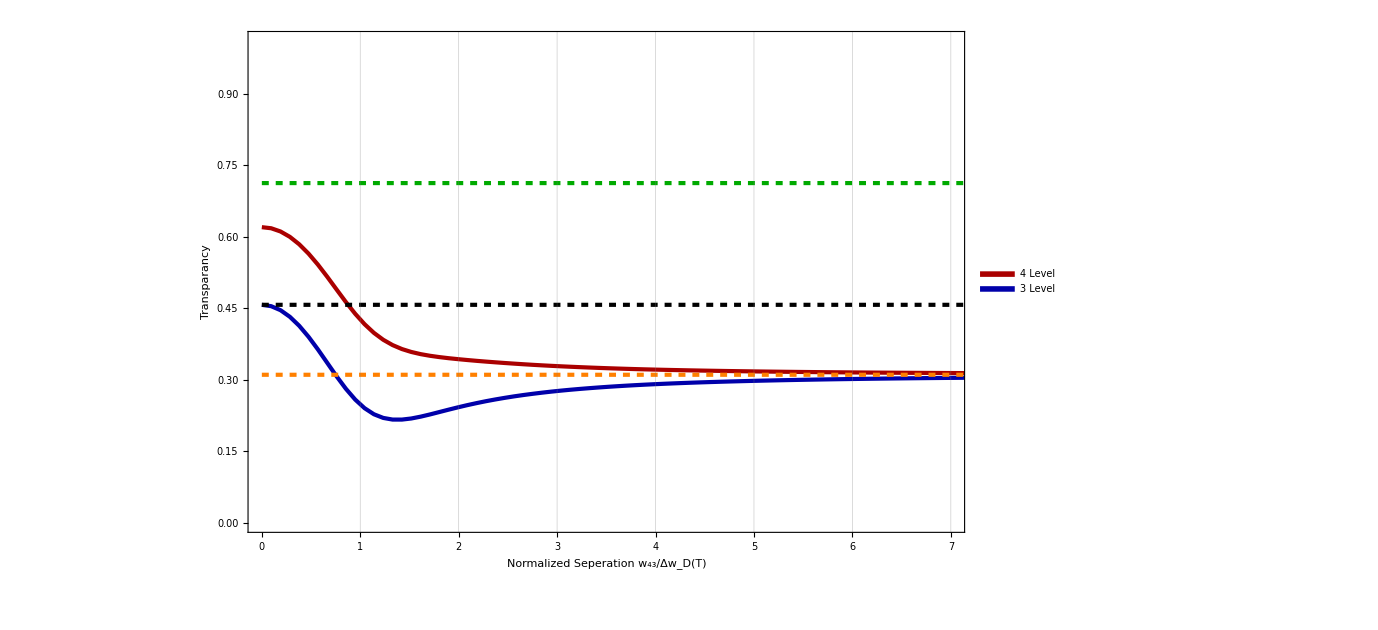

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Black],Style["3 Level",Black],Style["3 Level 42",Black],Style["3 level 32",Black],Style["3 level 32+42",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMM=ListPlot[{a2[[2]],a2[[1]],a2[[3]],a23,a24},PlotLegends->Placed[legend,{0.8,0.85}],ImageSize->1020,Joined->True,PlotStyle->{{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Orange,Dashed},{AbsoluteThickness[3],Darker[Green],Dashed},{AbsoluteThickness[3],Black,Dashed}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},PlotRange->{{0,7},{0,1.01}}]
```

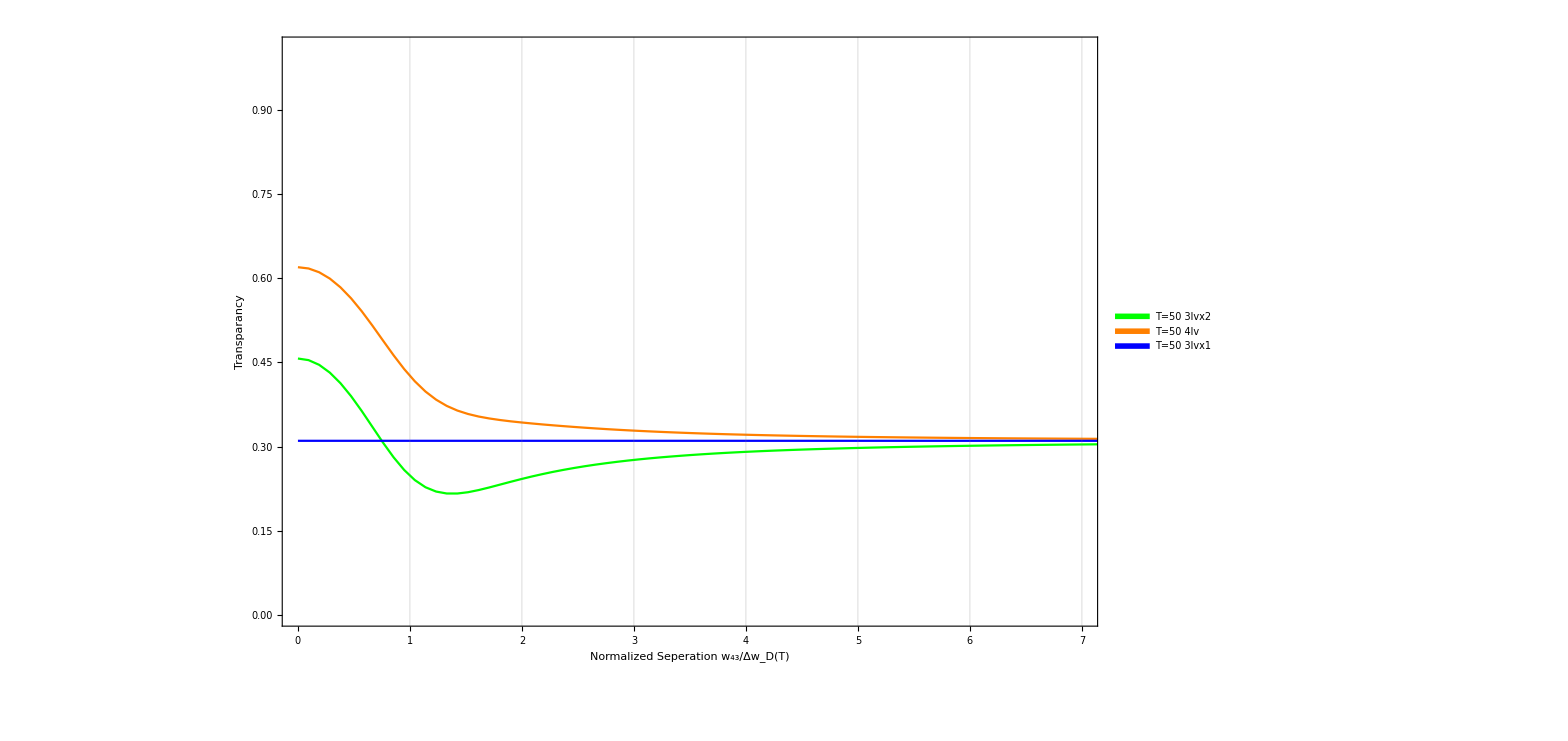

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\GoodFigure"]
Export["Figure9TvsSepHiDch.eps",MMM]
Export["Figure9TvsSepLowDch.eps",MMM2]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\GoodFigure

Figure9TvsSepHiDch.eps

Figure9TvsSepLowDch.eps

## test

```mathematica
Manipulate[ListPlot[Lev3DoppTestscSep[T,15.865/1000,1/1000,1*10^6,0,0,0,361*1000]/Lev3DoppTestscSep[T,0/1000,1/1000,1*10^6,0,0,0,361*1000],Joined->True,PlotRange->All],{T,0,200}]
```

```mathematica
γ=1.438;
step=0.05;
end=2;
p=15.865;
max3[i_]:=Mean[Lev3DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max4[i_]:=Mean[Lev4DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];max5[i_]:=Mean[Lev3x1DoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
max6[i_]:=Mean[Lev3xsingleDoppTestscSep[50,0/1000,1/1000,γ*10^6,0,0,0,i*1000]];
a2={Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[Lev3DoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]/max3[i]},{i,0.0001,end,step}], Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev4DoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max4[i]},{i,0.0001,end,step}],
Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3xsingleDoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max5[i]},{i,0.0001,end,step}]
};
```

```mathematica
a23=Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3xsingleDoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max6[i]},{i,0.0001,end,step}]
a24=Table[{i/(Rbpress[50][[2]]*10^-9),1-Min[fil[Lev3xsingleDoppTestscSep[50,p/1000,1/1000,γ*10^6,0,0,0,i*1000]]]/max3[i]},{i,0.0001,end,step}]
```

{{0.000189785,0.310276},{0.0950824,0.310276},{0.189975,0.310276},{0.284868,0.310276},{0.37976,0.310276},{0.474653,0.310276},{0.569546,0.310276},{0.664438,0.310276},{0.759331,0.310276},{0.854224,0.310276},{0.949116,0.310276},{1.04401,0.310276},{1.1389,0.310276},{1.23379,0.310276},{1.32869,0.310276},{1.42358,0.310276},{1.51847,0.310276},{1.61336,0.310276},{1.70826,0.310276},{1.80315,0.310276},{1.89804,0.310276},{1.99294,0.310276},{2.08783,0.310276},{2.18272,0.310276},{2.27761,0.310276},{2.37251,0.310276},{2.4674,0.310276},{2.56229,0.310276},{2.65718,0.310276},{2.75208,0.310276},{2.84697,0.310276},{2.94186,0.310276},{3.03675,0.310276},{3.13165,0.310276},{3.22654,0.310276},{3.32143,0.310276},{3.41632,0.310276},{3.51122,0.310276},{3.60611,0.310276},{3.701,0.310276}}

{{0.000189785,0.616821},{0.0950824,0.614003},{0.189975,0.605607},{0.284868,0.59176},{0.37976,0.572743},{0.474653,0.54908},{0.569546,0.521624},{0.664438,0.491611},{0.759331,0.460612},{0.854224,0.430372},{0.949116,0.402539},{1.04401,0.378384},{1.1389,0.358604},{1.23379,0.343287},{1.32869,0.332038},{1.42358,0.324173},{1.51847,0.318915},{1.61336,0.315543},{1.70826,0.313458},{1.80315,0.31221},{1.89804,0.311483},{1.99294,0.311067},{2.08783,0.310831},{2.18272,0.310696},{2.27761,0.310615},{2.37251,0.310565},{2.4674,0.31053},{2.56229,0.310505},{2.65718,0.310484},{2.75208,0.310468},{2.84697,0.310453},{2.94186,0.310441},{3.03675,0.310429},{3.13165,0.31042},{3.22654,0.310411},{3.32143,0.310402},{3.41632,0.310395},{3.51122,0.310388},{3.60611,0.310382},{3.701,0.310377}}

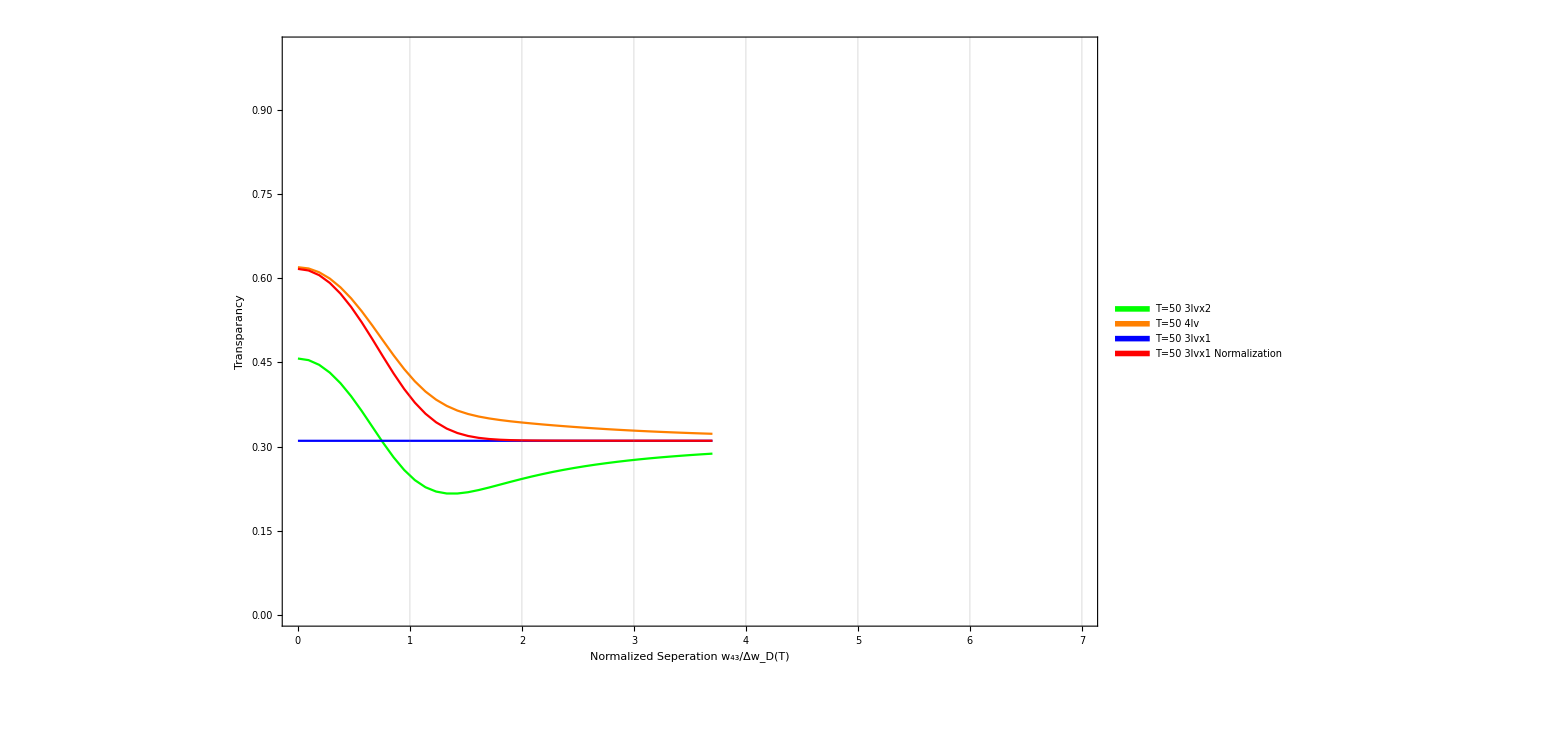

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red},AbsoluteThickness[5]]],{Style["T=50 3lvx2",Black],Style["T=50 4lv",Black],Style["T=50 3lvx1",Black],Style["T=50 3lvx1 Normalization",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->30}];
MMM=ListPlot[{a2[[1]],a2[[2]],a23,a24},PlotLegends->Placed[legend,{Right,Center}],ImageSize->1200,Joined->True,PlotStyle->{Green,Orange,Blue,Red,Black},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[30],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},PlotRange->{{0,7},{0,1.01}}]
```

# Test

```mathematica
Lev4DoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,Sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Range[-0.01,0.01,0.0002])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(Sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

(*Re[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Re[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]*)
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]

,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
(*{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}*)
]
]
```

```mathematica
Lev3DoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.0002])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]

,
If[ab==2,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}]
]]
```

```mathematica
Lev3x1DoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.0002])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ+w43,0,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]

,
If[ab==2,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,0,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,0,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}]
]]
```

```mathematica
Lev3xsingleDoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.0002])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]

,
If[ab==2,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,0,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}]
]]
```

```mathematica
Manipulate[
ListPlot[{Lev3x1DoppTestscSep[20,50/1000,1/1000,γ*10^6,0,0,2,i*1000],Lev3DoppTestscSep[20,50/1000,1/1000,γ*10^6,0,0,2,i*1000],Lev4DoppTestscSep[20,50/1000,1/1000,γ*10^6,0,0,2,i*1000],Lev3xsingleDoppTestscSep[20,50/1000,1/1000,γ*10^6,0,0,2,i*1000]},Joined->True,PlotRange->{0.88,1},PlotLegends->{"3x1","3x2","4","3Sing"}]
,{i,0,20}]
```

Transpose::nmtx: The first two levels of {{-0.01,-0.0098,-0.0096,-0.0094,-0.0092,-0.009,-0.0088,-0.0086,-0.0084,-0.0082,-0.008,-0.0078,-0.0076,-0.0074,-0.0072,-0.007,-0.0068,-0.0066,-0.0064,-0.0062,«11»,-0.0038,-0.0036,-0.0034,-0.0032,-0.003,-0.0028,-0.0026,-0.0024,-0.0022,-0.002,-0.0018,-0.0016,-0.0014,-0.0012,-0.001,-0.0008,-0.0006,-0.0004,-0.0002,«51»},ⅇ^(«1»)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

Statistics`Library`MatrixRowTranslate::ovfl: Overflow occurred in computation.

Set::pkspec1: The expression {1,31,41,42,43,44,45,46,47,48,58,57,56,55,54,53,52,51,61,91,11,21,22,32,33,34,35,49,Overflow[],59,65,64,63,62,72,71,81,5,15,25,75,85,95} cannot be used as a part specification.

```mathematica
Manipulate[
ListPlot[Lev3x1DoppTestscSep[20,50/1000,1/1000,γ*10^6,0,0,1,i*1000],Joined->True,PlotRange->All]
,{i,0,2}]
```

ListPlot::lpn: Lev3x1DoppTestscSep[20.,0.05,0.001,1.×10^6 γ,0.,0.,1.,268.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{-0.01,-0.0098,-0.0096,-0.0094,-0.0092,-0.009,-0.0088,-0.0086,-0.0084,-0.0082,-0.008,-0.0078,-0.0076,-0.0074,-0.0072,-0.007,-0.0068,-0.0066,-0.0064,-0.0062,«11»,-0.0038,-0.0036,-0.0034,-0.0032,-0.003,-0.0028,-0.0026,-0.0024,-0.0022,-0.002,-0.0018,-0.0016,-0.0014,-0.0012,-0.001,-0.0008,-0.0006,-0.0004,-0.0002,«51»},«18»} cannot be transposed.

Transpose::nmtx: The first two levels of {{-0.01,-0.0098,-0.0096,-0.0094,-0.0092,-0.009,-0.0088,-0.0086,-0.0084,-0.0082,-0.008,-0.0078,-0.0076,-0.0074,-0.0072,-0.007,-0.0068,-0.0066,-0.0064,-0.0062,«11»,-0.0038,-0.0036,-0.0034,-0.0032,-0.003,-0.0028,-0.0026,-0.0024,-0.0022,-0.002,-0.0018,-0.0016,-0.0014,-0.0012,-0.001,-0.0008,-0.0006,-0.0004,-0.0002,«51»},ⅇ^(«1»)} cannot be transposed.

Transpose::nmtx: The first two levels of {{-0.01,-0.0098,-0.0096,-0.0094,-0.0092,-0.009,-0.0088,-0.0086,-0.0084,-0.0082,-0.008,-0.0078,-0.0076,-0.0074,-0.0072,-0.007,-0.0068,-0.0066,-0.0064,-0.0062,«11»,-0.0038,-0.0036,-0.0034,-0.0032,-0.003,-0.0028,-0.0026,-0.0024,-0.0022,-0.002,-0.0018,-0.0016,-0.0014,-0.0012,-0.001,-0.0008,-0.0006,-0.0004,-0.0002,«51»},(«44»)^(«1»)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Lev3x1DoppTestscSep[20.,0.05,0.001,1.438×10^6,0.,0.,1.,268.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[Lev3DoppTestscSep[20,50/1000,1/1000,γ*10^6,0,0,1,i*1000],Joined->True,PlotRange->All]
,{i,0,2}]
```

Transpose::nmtx: The first two levels of {{-0.01,-0.0098,-0.0096,-0.0094,-0.0092,-0.009,-0.0088,-0.0086,-0.0084,-0.0082,-0.008,-0.0078,-0.0076,-0.0074,-0.0072,-0.007,-0.0068,-0.0066,-0.0064,-0.0062,«11»,-0.0038,-0.0036,-0.0034,-0.0032,-0.003,-0.0028,-0.0026,-0.0024,-0.0022,-0.002,-0.0018,-0.0016,-0.0014,-0.0012,-0.001,-0.0008,-0.0006,-0.0004,-0.0002,«51»},ⅇ^(«1»)} cannot be transposed.

Transpose::nmtx: The first two levels of {{-0.01,-0.0098,-0.0096,-0.0094,-0.0092,-0.009,-0.0088,-0.0086,-0.0084,-0.0082,-0.008,-0.0078,-0.0076,-0.0074,-0.0072,-0.007,-0.0068,-0.0066,-0.0064,-0.0062,«11»,-0.0038,-0.0036,-0.0034,-0.0032,-0.003,-0.0028,-0.0026,-0.0024,-0.0022,-0.002,-0.0018,-0.0016,-0.0014,-0.0012,-0.001,-0.0008,-0.0006,-0.0004,-0.0002,«51»},(«44»)^(«1»)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[Lev3xsingleDoppTestscSep[20,50/1000,1/1000,γ*10^6,0,0,1,i*1000],Joined->True,PlotRange->All]
,{i,0,2}]
```

ListPlot::lpn: Lev3xsingleDoppTestscSep[20.,0.05,0.001,1.×10^6 γ,0.,0.,1.,0.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.